## Data

```mathematica
(*kitti15=ResourceData["https://www.wolframcloud.com/obj/pierre-andre.brousseau/DeployedResources/Data/Kitti15-Stereo/"]*)
(*Export["Kitti15.wl", kitti15];*)
kitti15 = Import["Kitti15.wl"]
```

```mathematica
data=RandomSample[kitti15 ];
dataTrain=data[[1;;120]];
dataValid=data[[121;;160]];
dataTest=data[[161;;200]];
{w,h}=ImageDimensions[dataTrain[[1,"iLeft"]]]
```

{311,94}

## Neural Network

### Cost Volume

My personnal implementation of 
https://github.com/JiaRenChang/PSMNet/blob/master/models/stackhourglass.py
The original code uses For loops which require Table in mathematica. FunctionLayer does not yet support Table.

```mathematica
Clear[replicateLeft,rotateRight,featuresToCost]
replicateLeft[maxDisp_]:=NetChain[{
ReplicateLayer[maxDisp+1],
FunctionLayer[Transpose[#,{2,1,3,4}]&]
}]
rotateRight[features_,maxDisp_,{heigth_,width_}]:=NetGraph[Join[
{PaddingLayer[{{0,0},{0,0},{maxDisp,0}},"Fixed"]},
Table[
FunctionLayer[{#[[All,All,1-d+maxDisp;;width-d+maxDisp]]}&],
{d,0,maxDisp}],
{CatenateLayer[]},
{FunctionLayer[Transpose[#,{2,1,3,4}]&]}
],{
NetPort["Input"]->1->Table[d,{d,2,maxDisp+2}]->maxDisp+3->maxDisp+4->NetPort["Output"]
},"Input"->{features,heigth,width}]
featuresToCost[features_,maxDisp_,{heigth_,width_}]:=NetGraph[FunctionLayer[Block[{left,right,concat},(
left=replicateLeft[maxDisp][#fLeft];
right=rotateRight[features,maxDisp,{heigth,width}][#fRight];
concat=Join[left,right]
)]&, "fLeft"->{features,heigth,width},"fRight"->{features,heigth,width}]]
```

### Convolution 2D

```mathematica
Clear[conv2Dbn];
conv2Dbn[f_,{kx_,ky_},{sx_,sy_},{dx_,dy_}]:=NetGraph[FunctionLayer[Block[{pad,c,bn,relu},(
pad=PaddingLayer[{{0,0},{Floor[kx/2]*dx,Floor[kx/2]*dx},{Floor[ky/2]*dy,Floor[ky/2]*dy}},Padding->"Fixed"][#Input];
c=ConvolutionLayer[f,{kx,ky},"Stride"->{sx,sy},"Dilation"->{dx,dy}, "Biases"->None][pad];
bn=BatchNormalizationLayer[][c];
relu=Ramp[bn];
<|"Output"->relu|>
)]&]]
conv2Dbn[f_,{kx_,ky_},{sx_,sy_}]:=conv2Dbn[f,{kx,ky},{sx,sy},{1,1}]
conv2Dbn[f_,{kx_,ky_}]:=conv2Dbn[f,{kx,ky},{1,1}]
conv2Dbn[f_Integer]:=conv2Dbn[f,{3,3}]
```

### Convolution 3D

```mathematica
Clear[conv3Dbn];
conv3Dbn[f_,{kx_,ky_,kz_},{sx_,sy_,sz_}]:=NetGraph[FunctionLayer[Block[{pad,c,bn,relu},(
pad=PaddingLayer[{{0,0},{Floor[kx/2],Floor[kx/2]},{Floor[ky/2],Floor[ky/2]},{Floor[kz/2],Floor[kz/2]}},Padding->"Fixed"][#Input];
c=ConvolutionLayer[f,{kx,ky,kz},"Stride"->{sx,sy,sz}, "Biases"->None][pad];
bn=BatchNormalizationLayer[][c];
relu=Ramp[bn];
<|"Output"->relu|>
)]&]]
conv3Dbn[f_,{kx_,ky_,kz_}]:=conv3Dbn[f,{kx,ky,kz},{1,1,1}];
conv3Dbn[f_Integer]:=conv3Dbn[f,{3,3,3}]
```

### Disparity Regression

Implementation of
https://github.com/JiaRenChang/PSMNet/blob/master/models/submodule.py

```mathematica
dispRegression[maxDisp_]:=NetGraph[
FunctionLayer[Block[{dispRange,upsample,cost,transposed,probabilities,disparityMap},(
dispRange=NetArrayLayer["Array"->Range[0,maxDisp],LearningRateMultipliers->0][];
cost=#Input[[1]];
transposed=Transpose[cost,{3,1,2}];
probabilities=SoftmaxLayer[3][transposed];
disparityMap=probabilities.dispRange
)]&]]
```

### Disparity Estimator

```mathematica
Clear[disparityNet];
disparityNet[maxDisp_,{heigth_,width_}]:=NetGraph[Block[{featureExtractionLayer,costVolumeLayer,CNN3DLayer,dispRegressionLayer},(
(*__init__*)

featureExtractionLayer=NetInsertSharedArrays[NetChain[{conv2Dbn[16],conv2Dbn[16],conv2Dbn[32],conv2Dbn[32]}],"encoder"];
costVolumeLayer=featuresToCost[32,maxDisp,{heigth,width}];
CNN3DLayer=NetChain[{conv3Dbn[32],conv3Dbn[32],PaddingLayer[{{0,0},{1,1},{1,1},{1,1}},Padding->"Fixed"],ConvolutionLayer[1,{3,3,3},"Biases"->None]}];
dispRegressionLayer=dispRegression[maxDisp];
(*call/forward*)
FunctionLayer[Block[{featuresLeft,featuresRight,costVolume,processedCost,disparity},(
featuresLeft=featureExtractionLayer[#iLeft];
featuresRight=featureExtractionLayer[#iRight];
costVolume=costVolumeLayer[<|"fLeft"->featuresLeft,"fRight"->featuresRight|>];
processedCost=CNN3DLayer[costVolume];
disparity=dispRegressionLayer@processedCost;
<|"Output"->{disparity}|>
)]&,"iLeft"->{3,heigth,width},"iRight"->{3,heigth,width}]
)]]
```

### L1Loss

```mathematica
Clear[L1Loss]
L1Loss[]:=NetGraph[
FunctionLayer[Block[{mask,diff,L1mask,L1,L2,n,mean},(
mask=UnitStep[#Target-Power[10,-6]];
diff=AggregationLayer[Total,All][Abs[#Input-#Target]*mask];
n=AggregationLayer[Total,All][mask];
mean=diff/n;
<|"Output"->mean|>
)]&]]
```

### Trainable Net

```mathematica
trainableNet[maxDisp_,{height_,width_}]:=NetGraph[Block[{encRGB,encGray,disparitynet,L1LossLayer},(
(*init*)
encRGB=NetEncoder[{"Image",{width,height},ColorSpace->"RGB"}];
encGray=NetEncoder[{"Image",{width,height},ColorSpace->"Grayscale"}];
disparitynet=disparityNet[maxDisp,{height,width}];
L1LossLayer=L1Loss[];
(*call/forward*)
FunctionLayer[Block[{disparity,loss},(
disparity=disparitynet[<|"iLeft"->#iLeft,"iRight"->#iRight|>];
loss=L1LossLayer[<|"Input"->disparity,"Target"->#iDispLeft|>];
<|"Output"->disparity,"Loss"->loss|>
)]&,"iLeft"->encRGB,"iRight"->encRGB,"iDispLeft"->encGray]
)]]
```

#### Data Augmentation

```mathematica
photometricAugmentation[image_]:=Module[{augmentedImage,brightnessShift,contrastFactor,gamma},
brightnessShift=RandomReal[{-0.5,0.5}];
augmentedImage=ImageAdjust[image,{brightnessShift,0,1}];
contrastFactor=RandomReal[{0.8,1.2}];
augmentedImage=ImageMultiply[augmentedImage,contrastFactor];
gamma=RandomReal[{0.8,1.2}];
augmentedImage=ImageApply[#^gamma&,augmentedImage];
augmentedImage];

augmentStereoPair[{iLeft_,iRight_}]:={photometricAugmentation[iLeft],photometricAugmentation[iRight]};


dataAugmented=Table[
<|
"iLeft"->photometricAugmentation[dataTrain[[i,"iLeft"]]],
"iRight"->photometricAugmentation[dataTrain[[i,"iRight"]]],
"iDispLeft"->dataTrain[[i,"iDispLeft"]] 
|>
,{i,Length[dataTrain]}];


dataExpanded=Join[dataTrain,dataAugmented];
```

## Training

```mathematica
tn=trainableNet[32,{h,w}]
```

NetGraph[…]

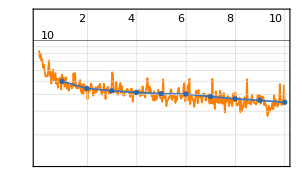
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:600  rounds:10  time:7.5min  examples/s:2.7
data | ,,  training examples:120  validation examples:40  processed examples:1200  skipped examples:0
method | ,,  ADAMoptimizer  batch size2GPU
round | ,,  loss:3.47
validation | ,,  loss:3.49
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
netTrainResult=
NetTrain[
tn,
dataAugmented,
All,
ValidationSet->dataValid,
BatchSize->2,
MaxTrainingRounds->10,
LossFunction->{"Loss"->Scaled[1]},
Method->{"ADAM",LearningRate->0.001},
TargetDevice->"GPU",
WorkingPrecision->"Real32"
]
```

## Test

```mathematica
trained=netTrainResult["TrainedNet"]
```

NetGraph[<2>, <6>]

```mathematica
pred[x_]:=Image[trained[x]["Output"],Interleaving->False];
```